# The Walking Dead

## Functions

```mathematica
SetDirectory[NotebookDirectory[]]
<<PajaroLocoPublic`
nonMigratoryForce=1000;
CalculateEuclideanDistances[coordinates_]:=Table[N[EuclideanDistance[coordinates[[i]],#]]&/@coordinates,{i,1,coordinates//Length }]
CalculateMigrationProbabilities[distancesMatrix_,nonMigratoryForce_]:=N[(#/Total[#])]&/@ReplaceAll[1/distancesMatrix//Quiet,ComplexInfinity->nonMigratoryForce]
ListPlotPoints[points_]:=ListPlot[points,
Frame->True,
Axes->True,
FrameStyle->Thickness[.005],
ImageSize->800,
FrameTicksStyle->None,
PlotStyle->PointSize[.025],
AspectRatio->1
]Options[EdgesStyleList2]:={LineThickness->.004,VariableStyle->"Both"}
EdgesStyleList2[vertexSyllableList_,OptionsPattern[]]:=Switch[OptionValue[VariableStyle],"LineColor",Table[DirectedEdge[vertexSyllableList[[i]][[1]][[1]],vertexSyllableList[[i]][[1]][[2]]]->{ColorData[{"LakeColors","Reverse"}][vertexSyllableList[[i]][[2]]],Thickness[OptionValue[LineThickness]]},{i,1,Length[vertexSyllableList]}],"LineWidth",Table[DirectedEdge[vertexSyllableList[[i]][[1]][[1]],vertexSyllableList[[i]][[1]][[2]]]->{Black,Thickness[vertexSyllableList[[i]][[2]]*OptionValue[LineThickness]]},{i,1,Length[vertexSyllableList]}],"Both",Table[DirectedEdge[vertexSyllableList[[i]][[1]][[1]],vertexSyllableList[[i]][[1]][[2]]]->{ColorData[{"LakeColors","Reverse"}][vertexSyllableList[[i]][[2]]],Thickness[vertexSyllableList[[i]][[2]]*OptionValue[LineThickness]]},{i,1,Length[vertexSyllableList]}],_,Table[DirectedEdge[vertexSyllableList[[i]][[1]][[1]],vertexSyllableList[[i]][[1]][[2]]]->{Thickness[OptionValue[LineThickness]]},{i,1,Length[vertexSyllableList]}]]
edgeshape[e_,___]:={Arrowheads[{{.0075,.5}}],Arrow[e]}
Options[GraphTransitionsFrequenciesWithMax]:={ImagePadding->None,Background->White,VertexStyle->Automatic,VertexCoordinates->Automatic,LineThickness->.0005,VariableStyle->"Both",GraphLayout->Automatic,Frame->False,FrameStyle->Thick,ImageSize->Automatic,VertexSize->.5,EdgeShapeFunction->edgeshape,VertexLabelStyle->{Italic},Prolog->{},Epilog->{},VertexShape->Automatic}
GraphTransitionsFrequenciesWithMax[frequenciesOutput_,max_,OptionsPattern[]]:=Module[{frequencies,syllables,edges,fixedEdgesList,vertexSyllableList,normalizedVertexSyllableList,edgesStyleList,links},frequencies=frequenciesOutput[[1]];
syllables=frequenciesOutput[[2]];
edges=Table[DirectedEdge[i,j]->frequencies[[i,j]],{i,Length[syllables]},{j,Length[syllables]}]//Flatten;
fixedEdgesList=DeleteCases[edges,DirectedEdge[_,_]->0];
vertexSyllableList=VertexNumberToVertexSyllable[frequenciesOutput[[2]],fixedEdgesList];
normalizedVertexSyllableList=(DirectedEdge[#[[1]],#[[2]][[1]]]->#[[2]][[2]]/max&)/@vertexSyllableList;
edgesStyleList=EdgesStyleList2[normalizedVertexSyllableList,LineThickness->OptionValue[LineThickness],VariableStyle->OptionValue[VariableStyle]];
links=DirectedEdge[#[[1]],#[[2,1]]]&/@vertexSyllableList;
Graph[syllables,links,
EdgeWeight->vertexSyllableList[[All,2,2]],
VertexStyle->OptionValue[VertexStyle],
EdgeStyle->edgesStyleList,
VertexCoordinates->OptionValue[VertexCoordinates],
ImageSize->OptionValue[ImageSize],
GraphLayout->OptionValue[GraphLayout],
EdgeShapeFunction->OptionValue[EdgeShapeFunction],
VertexShape->OptionValue[VertexShape],
VertexSize->OptionValue[VertexSize],
Frame->OptionValue[Frame],
FrameStyle->OptionValue[FrameStyle],
VertexLabelStyle->OptionValue[VertexLabelStyle],
VertexLabels->Placed["Name",Center],
EdgeLabels->Table[links[[i]]->Placed[fixedEdgesList[[All,2]][[i]],Tooltip],{i,Length[links]}],
Prolog->OptionValue[Prolog],
Epilog->OptionValue[Epilog],
Background->OptionValue[Background],
ImagePadding->OptionValue[ImagePadding],
PerformanceGoal->"Speed"
]
]
Themes`AddThemeRules["RandomPointsPlot",
AspectRatio->1,
Frame->True,
FrameLabel->(Style[#,20]&/@{"x (meters)","y (meters)"}),
FrameTicksStyle->20,
FrameStyle->Thick,
FrameTicks->{{None,All},{None,All}},
PlotStyle->Directive[PointSize[.02],Opacity[.75]],
AxesStyle->Directive[{Opacity[.25],Thick,Gray}]
]
Themes`AddThemeRules["RandomPointsMatrix",
AspectRatio->1,
Frame->True,
FrameStyle->Thick,
FrameTicks->{{None,None},{None,None}},
ColorFunction->"LakeColors",
AxesStyle->Directive[{Opacity[.25],Thick,Gray}]
]
DistributionIntoKernel[distribution_,center_,n_]:=Table[center+{Re[#],Im[#]}&[RandomReal[distribution] ⅇ^(ⅈ RandomReal[{0,2π}])],{n}]
MapDistributionParametersOnPoints[distribution_,centers_,n_]:=Join@@(DistributionIntoKernel[distribution,#,n]&/@centers)
SphereDistance[{ϕ1_,θ1_},{ϕ2_,θ2_},r_]:=r InverseHaversine[Haversine[ϕ1-ϕ2]+Cos[ϕ1]Cos[ϕ2]Haversine[θ1-θ2]]
SphereDistanceBetweenPoints[sphericalCoordinates1_,sphericalCoordinates2_]:=Module[{tuple},
tuple={
CoordinateTransformData["Cartesian"->"Spherical", "Mapping",sphericalCoordinates1],
CoordinateTransformData["Cartesian"->"Spherical", "Mapping",sphericalCoordinates2]
};
SphereDistance[{tuple[[1,2]],tuple[[1,3]]},{tuple[[2,2]],tuple[[2,3]]},tuple[[1,1]]]
]
SmoothHistogramPlot[sampledCoordinatesLayer_,{imageSize_,imagePadding_},plotRange_]:=SmoothHistogram[sampledCoordinatesLayer,
PlotStyle->Directive[{Thickness[.01],Opacity[.5]}],
ImageSize->imageSize,
PlotRange->{plotRange[[1]],plotRange[[2]]},
AspectRatio->.075,
Axes->False,
FrameTicks->{None,None},
Filling->Bottom,
FrameLabel->None,
ImagePadding->imagePadding,
ImageSize->imageSize,
PlotTheme->"RandomPointsPlot"
]
ListPlotScatter[clusteredCoordinates_,{imageSize_,imagePadding_},plotRange_]:=
ListPlot[clusteredCoordinates,
FrameTicks->Automatic,
BaseStyle->15,
LabelStyle->Directive[10],
FrameLabel->{{None,Rotate["y [meters]",180Degree]},{None,"x [meters]"}},
PlotRange->{plotRange[[1]],plotRange[[1]]},
PlotTheme->"RandomPointsPlot",
PlotStyle->Directive[{PointSize[.025],Opacity[.5]}],
ImageSize->imageSize,
ImagePadding->imagePadding
]
GenerateAccumulatedCoordinates[coordinatesRange_,citiesNumber_]:=Module[{sampledCoordinates,citiesDummy,names,pops,cities},
(*Generate Random Coordinates*)
sampledCoordinates=citiesDummy = Accumulate[RandomReal[{-coordinatesRange,coordinatesRange}, {citiesNumber, 2}]];
names = ToString /@ Range[citiesDummy // Length];
pops = RandomInteger[1000, citiesDummy // Length];
cities = Transpose[{names, citiesDummy, pops}];
{sampledCoordinates,names,pops,cities}
]
SyllableToID[a_,labels_]:=Position[labels,a]
ConvertSyllablesToID[sample_,syllablesLabels_]:=Table[SyllableToID[sample[[i]],syllablesLabels],{i,1,Length[sample]}]//Flatten
InTuples[communitiesList_,syllablesLabels_]:=Module[{communitiesIndexes},communitiesIndexes=Map[(Map[Position[syllablesLabels,#]&,#]//Flatten)&,communitiesList];
Tuples[#,2]&/@communitiesIndexes]
ListPlotSong[sample_,syllablesLabels_,OptionsPattern[]]:=Module[{texts,g},texts=Graphics[Text[Style[ToString[#[[1]]],OptionValue[TextSize]],{(sample//Length)+10,#[[2]]},Automatic],AspectRatio->1]&/@({syllablesLabels,Range[syllablesLabels//Length]}//Transpose);
g=ListPlot[
If[OptionValue[Labeling]==True,Labeled[#[[1]],#[[2]]]&,Tooltip[#[[1]],#[[2]]]&]/@({ConvertSyllablesToID[sample,syllablesLabels],ToString/@sample}//Transpose),
ImageSize->OptionValue[ImageSize],
PlotStyle->Directive[Opacity[.75],PointSize[Medium]],
Filling->None,
AxesLabel->{"TimeStep","ID"},
PlotRange->{0,syllablesLabels//Length},
ImagePadding->50,
GridLines->Automatic,
GridLinesStyle->Directive[LightBlue],
Frame->True,
FrameStyle->Directive[Thick,Black],
FrameTicksStyle->20
];
Show[g,texts,PlotRange->{0,(syllablesLabels//Length)+1}]
]
CalculateInOutRatio[inOutList_]:=(inOutList[[1]]/(inOutList[[1]]+inOutList[[2]]))
ListPlotSongWithCommunities[sample_,communities_,colors_,OptionsPattern[]]:=Module[{frequencyOutput,inOutTotals,labels2,individualCommunitiesInOutRatios,texts,connectionsRules,connectionsWithLabels,rect,rectangles,listPlot,sortedCommunities,wrappers,communitiesIDs,wrappersID},
frequencyOutput=GetTransitionsFrequencies[sample];
inOutTotals=GetCommunitiesInOutTransitionsFrequencies[frequencyOutput,communities,CountLoops->OptionValue[CountLoops]];
labels2=communities//Flatten//DeleteDuplicates;
sortedCommunities=Table[SortBy[i,Position[labels2,#]&],{i,communities}];
wrappers={(#//First)&/@sortedCommunities,(#//Last)&/@sortedCommunities}//Transpose;
communitiesIDs=Table[Position[labels2,#]&/@i//Flatten,{i,sortedCommunities}];
wrappersID={(#//First)&/@communitiesIDs,(#//Last)&/@communitiesIDs}//Transpose;
connectionsRules=wrappersID;
connectionsWithLabels=(UndirectedEdge[labels2[[#[[1]]]],labels2[[#[[2]]]]])&/@connectionsRules;
rect=Rectangle[{0.5,#[[1]]},{(sample//Length)+.5,#[[2]]},RoundingRadius->0]&/@connectionsRules;
rectangles=Graphics[
{
EdgeForm[Directive[Dashing[RandomReal[{0,0}]],Thickness[RandomReal[{.00175,.00175}]],Opacity[.2],colors[[#[[3]]]]]],Opacity[.2],colors[[#[[3]]]],#[[1]]
}
,ImagePadding->500]&/@({rect,Table[i[[1]]/(labels2//Length),{i,wrappersID}],Range[wrappersID//Length]}//Transpose);
individualCommunitiesInOutRatios=CalculateInOutRatio[#]&/@(inOutTotals//Transpose);
texts=Graphics[Text[Style[ToString[PaddedForm[#[[1]],{4,4}]],Bold,OptionValue[TextSize]],{(sample//Length)/2,#[[2]]+.35},Automatic],AspectRatio->1]&/@({individualCommunitiesInOutRatios,connectionsRules[[All,1]]}//Transpose);
listPlot=ListPlotSong[sample,labels2,ImageSize->OptionValue[ImageSize],Labeling->OptionValue[Labeling],TextSize->OptionValue[TextSize]];
Show[{listPlot,rectangles,texts}//Flatten]
]
```

/Users/sanchez.hmsc/Documents/GitHub/MoNeT/Dev/HectorSanchez/WalkingDead

RandomPointsPlot

RandomPointsMatrix

## Inputs

```mathematica
{vertexSize,vertexLabelSize}={2.5,7.5};
(*Set the number of cities wanted, the x-y coordinates range to sample from, and the number of site types allowd*)
{citiesNumber,coordinatesRange,classesNumber}={50,100,2};
(*Assigns a class type to each point based on a random uniform distribution of probabilities and the number of types defined previously*)
(*Set a vector with the probabilities the walker has to stay in current node or move to the others. This vector is then rotated to generate the "partiteness" mask.*)
directionStrength=.95;
movementProbabilitiesVector={1-directionStrength,directionStrength};
(*The penalizations matrix is a type-based transitions matrix to be used as mask down the road*)
penalizationsMatrix=Table[RotateRight[movementProbabilitiesVector,i-1],{i,1,classesNumber}];
MatrixForm[penalizationsMatrix]
```

(0.05 | 0.95
0.95 | 0.05)

## Generate Random Spatial Setting

{{1,2,3,4,5,6,7,8,10,20,22,23,24,25},{9,11,12,13,15,16,18,19,21},{14,38,39,40,41,42,43,45,46,47,48,49,50},{17},{26,28,29,30},{27},{31,32,33,34,35},{36},{37},{44}}

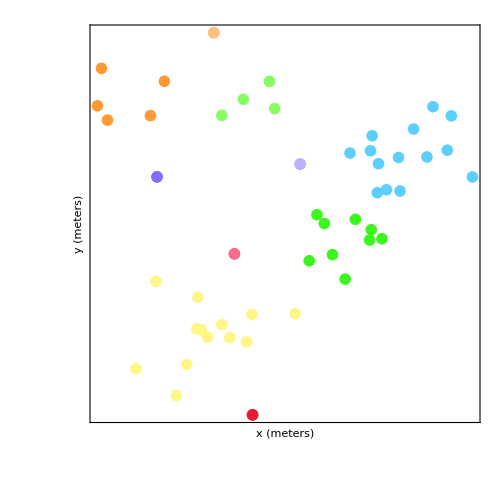

```mathematica
(*This is a very basic algorithm to generate points in a landscape. Replace it with a better later on.*)
{sampledCoordinates,names,pops,cities}=GenerateAccumulatedCoordinates[-100,citiesNumber];
distances = CalculateEuclideanDistances[sampledCoordinates];
(*Geo-Clustering*)
clusteredCoordinates=FindClusters[sampledCoordinates,Method->"NeighborhoodContraction"];
clustersStrings=Table[ToString/@Flatten[Position[cities[[All,2]],#]&/@clusteredCoordinates[[i]]],{i,1,clusteredCoordinates//Length}]
clustersIDs=Position[Map[ToExpression,clustersStrings,Infinity],#][[1,1]]&/@Range[Length[sampledCoordinates]];
(*Plots*)
colors=Reverse[ColorData["BrightBands",#]&/@Range[0,1,1/(Length[clustersStrings])]]//Flatten//RandomSample;
ListPlot[clusteredCoordinates,PlotTheme->"RandomPointsPlot",ImageSize->500,PlotStyle->colors]
```

## Analyze

Map

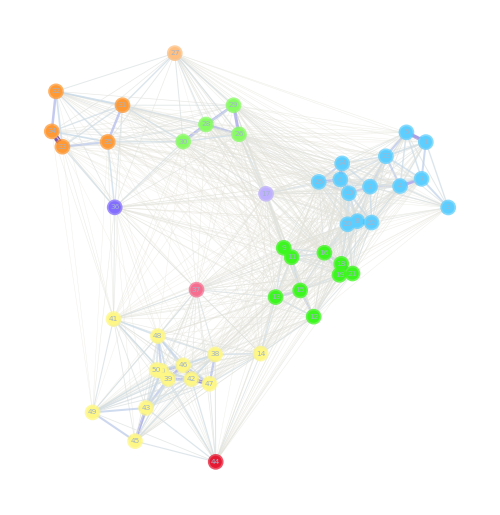

```mathematica
(*This "migration" is replacing the real kernel for the time being. It is based on the inverse of the distance to other nodes.*)
migration = CalculateMigrationProbabilities[distances, .05];
edgeshape2[e_,___]:={Arrowheads[{{.000001,.9}}],Arrow[e]}
stylesSwatch=Directive[Opacity[1],colors[[#]],EdgeForm[Directive[Opacity[.75],Thickness[.005]]]]&/@Range[clusteredCoordinates//Length];
stylesList=(ToString[#[[1]]]->stylesSwatch[[#[[2]]]])&/@Transpose[{Range[clustersIDs//Length],clustersIDs}];
map = GraphTransitionsFrequenciesWithMax[
  {
Chop[ReplacePart[migration,{i_,i_}->0]//LowerTriangularize,10^-2],
ToString /@ Range[Length[migration]]
   }, .15,
 VertexStyle ->stylesList,
VertexCoordinates ->sampledCoordinates,
VertexSize ->vertexSize,
VertexLabelStyle->vertexLabelSize,
ImageSize -> 500,
LineThickness -> .0075,
EdgeShapeFunction->edgeshape2,
VariableStyle->"Both"
  ]
```

Mask Movement with Site-Types

```mathematica
(*If the transition between city types is not possible, or improbable, then mask it with the corresponding value. After that, normalize for the probabilities to still add up to one.*)
cityType=RandomChoice[Range[classesNumber],citiesNumber]
{cityType[[1]],#}&/@cityType;
penalizationsMask=Table[penalizationsMatrix[[i,#]]&/@cityType,{i,cityType}];
normalizedMaskedMatrix=(#/Total[#])&/@(penalizationsMask*migration);
(*Plots*)
penalizationsMaskPlot=penalizationsMask//MatrixPlot[#,ColorFunction -> "LakeColors", ImageSize ->500/2]&;
colorsType=Reverse[ColorData["LakeColors",#]&/@Range[0,1,1/classesNumber]];
stylesSwatchType=Directive[Opacity[1],colorsType[[#]],EdgeForm[Directive[Opacity[.75],Thickness[.005]]]]&/@Range[classesNumber];
stylesListType=(ToString[#[[1]]]->stylesSwatchType[[#[[2]]]])&/@Transpose[{Range[cityType//Length],cityType}];
normalizedMaskedMatrixPlot=normalizedMaskedMatrix//MatrixPlot[#,ColorFunction->"LakeColors"]&;
```

{2,2,1,1,2,2,2,1,2,1,2,1,1,1,1,2,1,2,2,1,2,1,1,1,2,1,1,2,1,1,1,2,2,1,1,2,2,2,2,1,1,1,2,1,1,1,1,1,1,1}

Movement Network

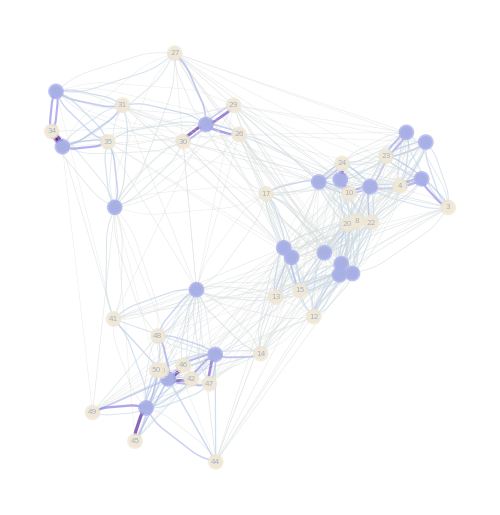

```mathematica
edgeshape2[e_,___]:={Arrowheads[{{.01,.75}}],Arrow[e]}
graph = GraphTransitionsFrequenciesWithMax[
  {
Chop[normalizedMaskedMatrix,10^-1.5],
ToString /@ Range[Length[normalizedMaskedMatrix]]
   }, .25,
 VertexStyle->stylesListType,
VertexCoordinates->sampledCoordinates,
VertexSize ->vertexSize,
VertexLabelStyle->vertexLabelSize,
ImageSize->500,
LineThickness->.005,
EdgeShapeFunction->edgeshape2,
VariableStyle->"Both"
  ]
```

Sink and Source

```mathematica
differenceThreshold=.3;
(**)
communities=Map[ToExpression,clustersStrings,Infinity]
outCommunity=Table[
comm=communities[[i]];
transitions=ReplacePart[normalizedMaskedMatrix,{i_,i_}->0];
Total[Total/@(Delete[transitions[[comm]]//Transpose,{#}&/@comm]//Transpose)]
,{i,1,Length[communities]}];
inCommunity=Table[
comm=communities[[i]];
transitions=ReplacePart[normalizedMaskedMatrix,{i_,i_}->0]//Transpose;
Total[Total/@(Delete[transitions[[comm]]//Transpose,{#}&/@comm]//Transpose)]
,{i,1,Length[communities]}];
outMinusIn=outCommunity-inCommunity;
typeOfCommunity=If[Abs[#]<differenceThreshold,"Bridge",If[#>0,"Source","Sink"]]&/@outMinusIn
(**)
gridSourceSink=Grid[{
Style[PaddedForm[#,{3,3}],7.5,Bold]&/@outMinusIn,
Style[#,7.5,Bold]&/@typeOfCommunity
},
Frame->True,Background->{Lighter[#,0.1]&/@colors[[1;;Length[outMinusIn]]],None},ItemSize->3]
edges=Table[colors[[i]]&/@clustersStrings[[i]],{i,1,Length[clustersStrings]}]//Flatten;
flattenedRatios=Table[ConstantArray[typeOfCommunity[[i]],communities[[i]]//Length],{i,1,communities//Length}]//Flatten;
graphSinkSource=HighlightGraph[graph, Style[#[[2]] ,Directive[EdgeForm[Directive[Opacity[1],Switch[#[[3]],"Bridge",Black,"Sink",Darker[Blue,0],"Source",Darker[Red,0]],Thickness[.005]]],#[[1]]]] & /@ ({edges,clustersStrings//Flatten,flattenedRatios} // Transpose)];
```

{{1,2,3,4,5,6,7,8,10,20,22,23,24,25},{9,11,12,13,15,16,18,19,21},{14,38,39,40,41,42,43,45,46,47,48,49,50},{17},{26,28,29,30},{27},{31,32,33,34,35},{36},{37},{44}}

{Sink,Sink,Source,Bridge,Source,Source,Source,Bridge,Sink,Source}

-1.370 | -1.770 |  0.928 |  0.247 |  0.539 |  0.535 |  0.789 | -0.122 | -0.355 |  0.582
Sink | Sink | Source | Bridge | Source | Source | Source | Bridge | Sink | Source

Sinks and Sources Report

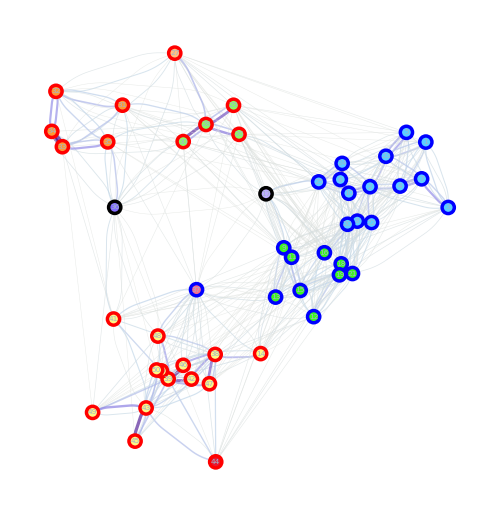
Clustered Map |  | Point Types |  | Sources (R) and Sinks(B)
-Graphics- | + | -Graphics- | = | -Graphics-
-1.370 | -1.770 |  0.928 |  0.247 |  0.539 |  0.535 |  0.789 | -0.122 | -0.355 |  0.582
Sink | Sink | Source | Bridge | Source | Source | Source | Bridge | Sink | Source

```mathematica
gridSinksAndSources=Grid[{
Style[#,25]&/@{"Clustered Map","","Point Types","","Sources (R) and Sinks(B)"},
{map,Style["+",Bold,50],graph,Style["=",Bold,50],Grid[{{graphSinkSource},{gridSourceSink}}]}
}]
```

Centrality Analysis

```mathematica
BetweennessCentrality[map]
a=HighlightGraph[map,VertexList[map],VertexSize-> Thread[VertexList[map]-> Rescale[%]]];
BetweennessCentrality[graph]
b=HighlightGraph[graph,VertexList[graph],VertexSize-> Thread[VertexList[graph]-> Rescale[%]]];
Grid[{{a,b}}]
```

{0.,1.24676,0.637376,1.42576,0.319099,3.91984,1.37697,4.76843,11.0975,3.92306,8.14269,19.3097,13.9407,10.6452,10.1207,7.25936,9.55068,7.25936,4.17769,2.92715,7.09485,1.35485,1.40621,3.32674,9.15463,6.3448,5.35358,6.44653,7.03052,11.2998,5.29806,2.49086,4.76512,2.51781,5.88931,40.4619,98.5302,21.9196,1.20411,0.,41.4884,0.339361,0.697016,9.12045,2.40503,0.339361,1.19074,2.05827,2.42386,0.}

{15.6688,33.7365,24.5933,35.4622,18.5923,48.0086,18.5923,51.6119,133.683,51.6119,162.813,75.146,88.8685,136.423,54.4579,92.9053,279.849,76.3082,126.87,51.6119,90.4291,51.6119,20.4468,51.6119,145.278,104.355,52.4296,93.3101,31.4813,27.8408,24.7082,35.5949,29.1842,4.64116,19.9867,246.775,303.563,83.207,51.3933,11.0157,81.7392,17.6107,208.087,13.29,5.35226,14.1577,40.0988,69.8878,13.5041,22.5947}

-Graphics-

```mathematica
ClosenessCentrality[map]
a=HighlightGraph[map,VertexList[map],VertexSize-> Thread[VertexList[map]-> Rescale[%]]];
ClosenessCentrality[graph]
b=HighlightGraph[graph,VertexList[graph],VertexSize-> Thread[VertexList[graph]-> Rescale[%]]];
Grid[{{a,b}}]
```

{0.,42.0519,27.8803,21.747,24.2745,40.068,24.1348,43.0384,56.9728,38.2794,45.2158,58.6906,42.0143,43.4978,34.6751,44.9495,48.1206,49.1844,34.1913,41.8517,38.4698,39.2401,49.1417,45.508,43.9419,61.5175,70.5502,59.9461,50.6927,52.1622,61.5609,56.3825,45.0207,34.8824,47.5166,54.3245,56.8059,41.9678,34.8907,29.8219,56.4236,35.2114,38.8712,46.2623,41.1531,35.2482,40.3372,41.9402,44.8251,36.3476}

{6.72635,7.12881,8.93003,9.12249,6.66903,9.11132,6.98844,8.00822,10.0414,8.84844,10.1989,9.92149,9.58248,10.4257,9.81628,9.76355,11.6803,10.0956,11.092,7.819,10.3994,8.14083,8.99122,9.23193,9.67693,12.9192,12.4333,9.06393,13.1165,10.9888,10.5422,9.66812,9.37284,7.24722,10.1099,11.3354,11.4634,8.51039,7.49533,7.87437,11.6214,8.81096,10.0253,11.6726,10.7798,8.63449,9.90934,10.2386,11.3279,7.50263}

-Graphics-

Walkers

```mathematica
kernel=normalizedMaskedMatrix;
initialState=ConstantArray[0,kernel//Length]//ReplacePart[#,3->1]&;
markov=DiscreteMarkovProcess[initialState,kernel];
```

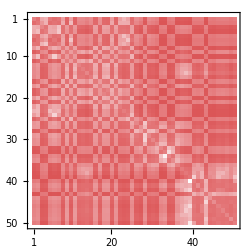
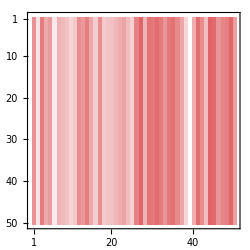
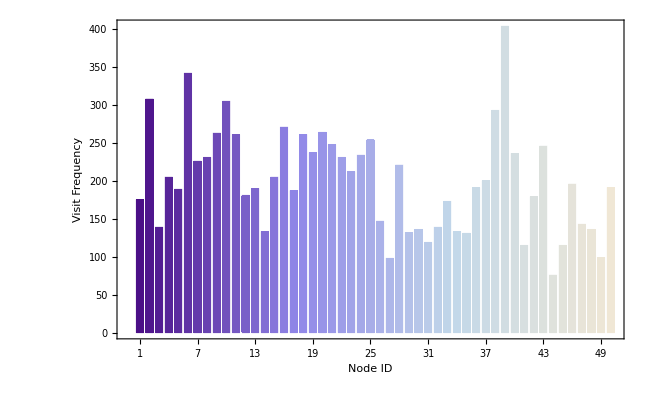
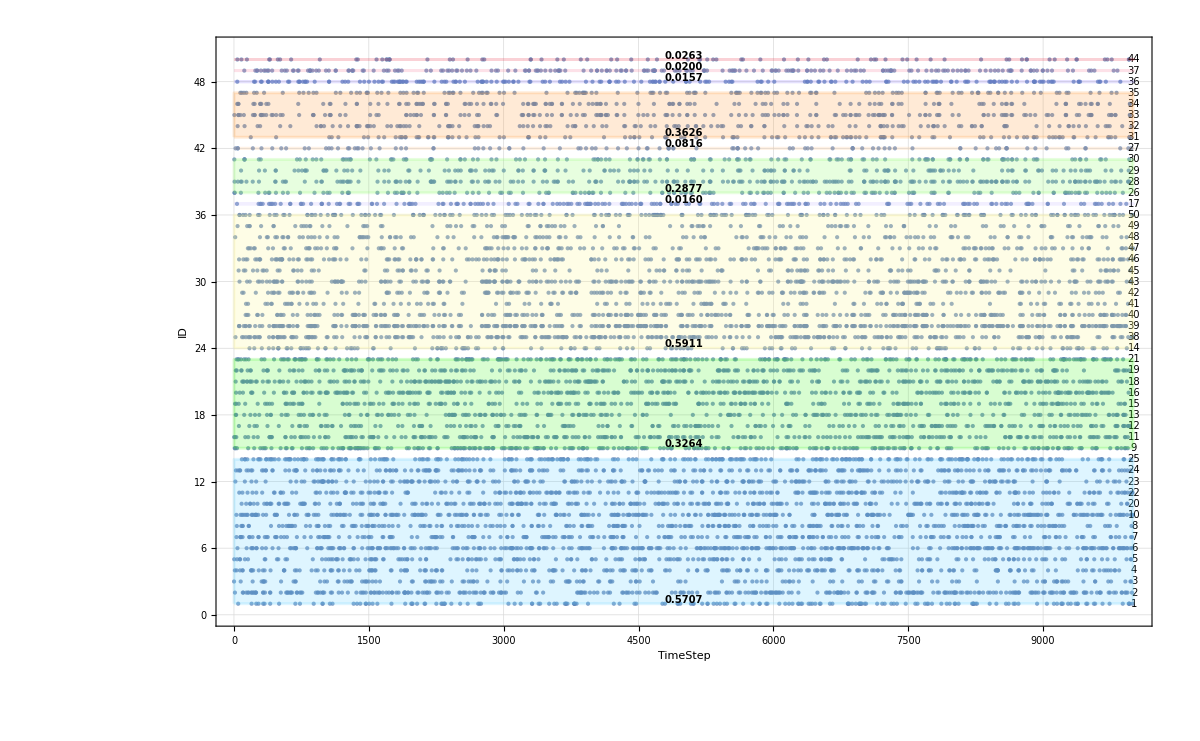
Transitions | Limiting
-Graphics- | -Graphics-
-Graphics- | -Graphics-

```mathematica
(**)
data=RandomFunction[markov,{0,10000}];
tally=(data//Normal)[[All,All,2]][[1]]//Tally//Sort;
barChartFrequency=BarChart[tally[[All,2]],
ChartStyle->"LakeColors",
ChartLabels->tally[[All,1]],
ImageSize->650,
Frame->True,
FrameStyle->Thick,
FrameTicksStyle->Directive[8],
FrameLabel->(Style[#,25]&/@{"Node ID","Visit Frequency"})
];
songs=ListPlotSongWithCommunities[(data//Normal)[[1,All,2]],Map[ToExpression,clustersStrings,Infinity],colors,ImageSize->1200,TextSize->10];
{Range[Length[kernel]],MarkovProcessProperties[markov,"HoldingTimeMean"]}//MatrixForm;
limitMatrix=MarkovProcessProperties[markov,"LimitTransitionMatrix"]//MatrixPlot[#,PlotLegends->Placed[Automatic,Below],ColorFunction->"CherryTones",ImageSize->250]&;
transitionsMatrix=MarkovProcessProperties[markov,"TransitionMatrix"]//MatrixPlot[#,PlotLegends->Placed[Automatic,Below],ColorFunction->"CherryTones",ImageSize->250]&;
matricesGrid=Grid[{Style[#,15]&/@{"Transitions","Limiting"},{transitionsMatrix,limitMatrix}}];
gridRandomWalker=Grid[{{Grid[{{matricesGrid},{barChartFrequency}}],songs}}]
```

Markov

```mathematica
MarkovProcessProperties[markov,"LimitTransitionMatrix"][[1]]
```

{0.0180681,0.0309849,0.014577,0.0219273,0.0191803,0.0328568,0.0230125,0.023813,0.0246715,0.027501,0.0256272,0.0176327,0.0187999,0.0146093,0.021785,0.0263356,0.0176676,0.0256328,0.0247753,0.0246354,0.0237193,0.021997,0.0210533,0.0242642,0.026821,0.0146741,0.00966523,0.0231283,0.0134383,0.0142643,0.0112199,0.0144548,0.0187437,0.0143538,0.0124444,0.0169251,0.0217798,0.0279711,0.0407546,0.0221589,0.011553,0.0175158,0.024383,0.00942424,0.0110777,0.0184255,0.0156923,0.0146365,0.00983544,0.0195322}

```mathematica
trans=Transpose[kernel];
{eVals,eVecs}=Eigensystem[trans]//N;
Normalize[eVecs[[1]],Total]
```

{0.0180681,0.0309849,0.014577,0.0219273,0.0191803,0.0328568,0.0230125,0.023813,0.0246715,0.027501,0.0256272,0.0176327,0.0187999,0.0146093,0.021785,0.0263356,0.0176676,0.0256328,0.0247753,0.0246354,0.0237193,0.021997,0.0210533,0.0242642,0.026821,0.0146741,0.00966523,0.0231283,0.0134383,0.0142643,0.0112199,0.0144548,0.0187437,0.0143538,0.0124444,0.0169251,0.0217798,0.0279711,0.0407546,0.0221589,0.011553,0.0175158,0.024383,0.00942424,0.0110777,0.0184255,0.0156923,0.0146365,0.00983544,0.0195322}

{0.0180681,0.0309849,0.014577,0.0219273,0.0191803,0.0328568,0.0230125,0.023813,0.0246715,0.027501,0.0256272,0.0176327,0.0187999,0.0146093,0.021785,0.0263356,0.0176676,0.0256328,0.0247753,0.0246354,0.0237193,0.021997,0.0210533,0.0242642,0.026821,0.0146741,0.00966523,0.0231283,0.0134383,0.0142643,0.0112199,0.0144548,0.0187437,0.0143538,0.0124444,0.0169251,0.0217798,0.0279711,0.0407546,0.0221589,0.011553,0.0175158,0.024383,0.00942424,0.0110777,0.0184255,0.0156923,0.0146365,0.00983544,0.0195322}

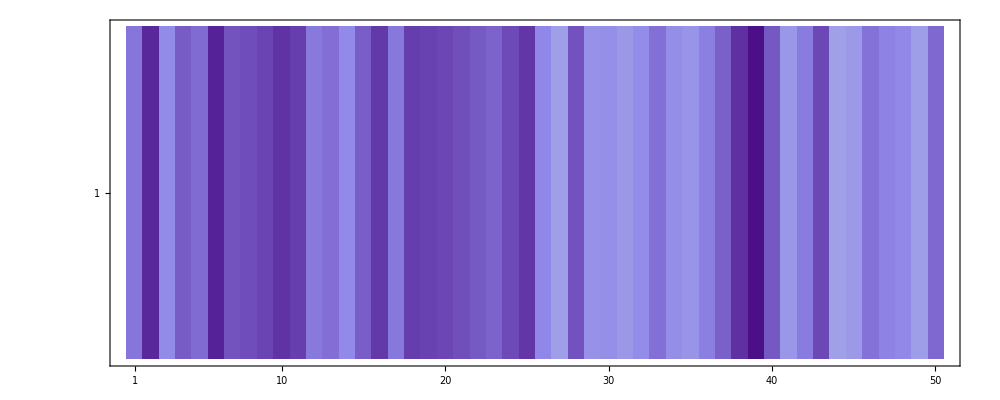

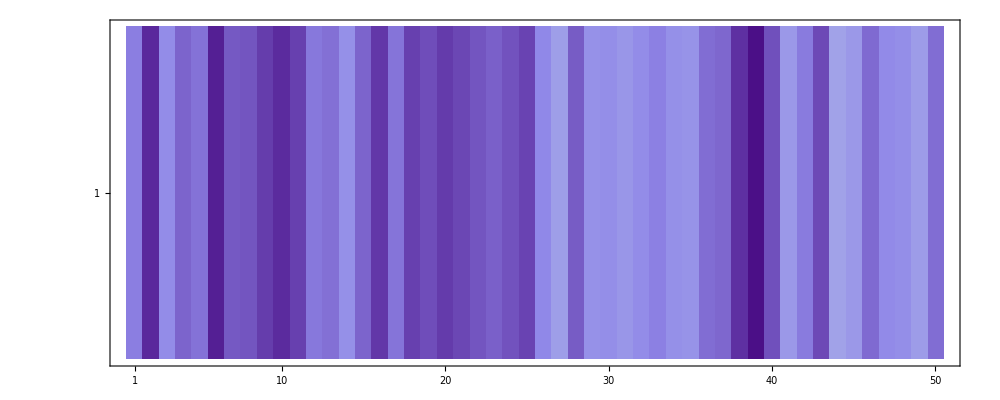

```mathematica
markov=DiscreteMarkovProcess[initialState,kernel];
markovPDF=PDF[StationaryDistribution[markov],#]&/@Range[markov[[1]]//Length]
MatrixPlot[{markovPDF},ColorFunction->ColorData[{"LakeColors","Reverse"}],ImageSize->1000]
MatrixPlot[{tally[[All,2]]},ColorFunction->ColorData[{"LakeColors","Reverse"}],ImageSize->1000]
```

```mathematica
{Range[markov[[1]]//Length],markovPDF}//Transpose
```

{{1,0.0180681},{2,0.0309849},{3,0.014577},{4,0.0219273},{5,0.0191803},{6,0.0328568},{7,0.0230125},{8,0.023813},{9,0.0246715},{10,0.027501},{11,0.0256272},{12,0.0176327},{13,0.0187999},{14,0.0146093},{15,0.021785},{16,0.0263356},{17,0.0176676},{18,0.0256328},{19,0.0247753},{20,0.0246354},{21,0.0237193},{22,0.021997},{23,0.0210533},{24,0.0242642},{25,0.026821},{26,0.0146741},{27,0.00966523},{28,0.0231283},{29,0.0134383},{30,0.0142643},{31,0.0112199},{32,0.0144548},{33,0.0187437},{34,0.0143538},{35,0.0124444},{36,0.0169251},{37,0.0217798},{38,0.0279711},{39,0.0407546},{40,0.0221589},{41,0.011553},{42,0.0175158},{43,0.024383},{44,0.00942424},{45,0.0110777},{46,0.0184255},{47,0.0156923},{48,0.0146365},{49,0.00983544},{50,0.0195322}}

```mathematica
HighlightGraph[graph,VertexList[graph],VertexSize-> Thread[VertexList[graph]->2*Rescale[markovPDF]]]
```

-Graphics-

## Export Report

```mathematica
Grid[{{gridSinksAndSources},{gridRandomWalker}}]
Export["NetworkReport"<>StringPadLeft[ToString[(directionStrength*100)//Round],3,"0"]<>".pdf",%,ImageSize->5000,ImageResolution->500]
```